# Accuracy and Numerical Stability

We have seen a number of Numerical ODE solvers so far.  We have the BDF family, we have the Taylor series family, we have Pade generalizations of Taylor series solvers, and we have two old favorites (Implicit and Explicit Euler) and a few others that are the simplest cases of several families.

The hope is that fancier solvers will let us maintain accuracy with larger steps.  We restrict attention to autonomous ODE systems y'=f(y) on ℝ^n with f(0)=y_0∈ℝ^n and assume that f is as smooth as is required for our computations.

## Theorems and Definitions.

### Smoothness

If y'=f(y) and f(0)=x  then 
	y''=Df(y).y'  and J'=Df(y).J(y) with J(0)=I_n
where Df:ℝ^n→ℝ^(n×n) is the Jacobian matrix and J(t)=∇_x y(t) is the gradient of the solutions with respect to the initial condition. This process can be continued to higher derivatives provided f is sufficiently smooth and you are willing to deal with higher order tensors e.g.
	DDf:ℝ^n→ℝ^(n×n×n).
A consequence: 
1) If f is smooth with k continuous derivatives then the solution y is smooth with k+1 derivatives.
2) There is no point in using a numerical solver that relies on smoothness unless the solution is smooth.   
3) Asymptotic error results only apply to smooth problems.

### Stiffness

According to Wikipedia
 https://en.wikipedia.org/wiki/Stiff_equation
“In mathematics, a stiff equation is a differential equation for which certain numerical methods for solving the equation are numerically unstable, unless the step size is taken to be extremely small. It has proven difficult to formulate a precise definition of stiffness, but the main idea is that the equation includes some terms that can lead to rapid variation in the solution.”  
My interpretation “Stiff ODEs are hard!”

According to Cleve Moler
 https://www.mathworks.com/company/technical-articles/stiff-differential-equations.html
“Stiffness is a subtle, difficult, and important - concept in the numerical solution of ordinary differential equations.
…
An ordinary differential equation problem is stiff if the solution being sought is varying slowly, but there are nearby solutions that vary rapidly, so the numerical method must take small steps to obtain satisfactory results.”

What we want are: 
1) Practical tests for stiffness.
2) Practical ode solvers if we suspect stiffness.
3) An understanding of the subtle, difficult, and important concept.

### Stiffness for Linear ODEs: Examples

Example:By any practical definition y'=A.y+f is stiff for almost any initial condition with
	A=(-3.11415×10^9 | 3.14954×10^9 | 3.3947×10^9
3.14954×10^9 | -3.18534×10^9 | -3.43328×10^9
3.3947×10^9 | -3.43328×10^9 | -3.70051×10^9)
and 
	f(t)=sin(t)(0.564388
0.558046
0)
Lets try to understand this claim.

### Stiffness Ratio for y'=A.y+g

The solution of y'=A.y with y(0)=y_0 is 
	y(t)=ⅇ^(A t).y_0
where if A is diagonalizable with eigen decomposition A=V.Λ.V^-1 then
	ⅇ^(A t)= V.ⅇ^Λt.V^-1 with ⅇ^(Λ t)=(ⅇ^(λ_1 t) |  |  | 
 | ⅇ^(λ_2 t) |  | 
 |  | ⋱ | 
 |  |  | ⅇ^(λ_n t))
A) If an eigenvalue λ=r is real there is a solution component ~ⅇ^(r t).  
	This component decays if r<0 and decays fast if r<<-1.
	This component grows if r>0 and grows fast if r>>1.
B) If an eigenvalue λ=a±ⅈ b is complex there are solution components ~ⅇ^(a t)cos(b t) and ~ⅇ^(a t)cos(b t)
  	These components decay if a<0 and decays fast if a<<-1.
	These components grow if a>0 and grow fast if a>>1.
	They oscillate rapidly if |b| >> 1
C) Components that decay rapidly compared to others become insignificant after a short period of time.  However, because the ODE is the same there are nearby solutions that would decay rapidly.  Sadly explicit solvers are always ready to react to the fastest time scales in an ODE. 
D) If all the eigenvalues λ_i have Re(λ_i)<0 the ratio of the fastest to the slowest exponential decay rate
	(max_(1≤i≤n) Re(-λ_i))/(min_(1≤i≤n) Re(-λ_i)) 
is the stiffness ratio.   
E) A linear problem is definitely stiff if all eigenvalues have negative real part and the stiffness ratio is large.

### Stiffness for y'=f(y)

The ODE y'=f(y) is definitely stiff at y_0 if all the eigenvalues of Df(y_0) have negative real part and the stiffness ratio is large. The argument is that near y_0 the linearized ODE z'=f(y_0)+Df(y_0).z approximates the behavior of the ODE.

Stiffness is an efficiency problem.  If the stiffness ratio is 10^5 then a non-stiff solver will have to take 10^5 times as many steps as carefully designed stiff solver.

With m=500 the stiffness ratio of the standard 3pt FD approximation matrix for u_xx is ~10^5.  The standard ODE  y'=A.y approximation for the heat equation is stiff.  Almost all ODEs that arise from such PDE semi-discretizations are stiff.

```mathematica
m=500;
A3=(m+1)^2 SparseArray[{Band[{1,1}]->-2.0,Band[{1,2}]->1.0,Band[{2,1}]->1.0},{m,m}];
A5=12(m+1)^2 SparseArray[{
Band[{1,1}]->-30.0,
Band[{1,2}]->16.0,Band[{2,1}]->16.0,
Band[{1,3}]->-1.0,Band[{3,1}]->-1.0
},{m,m}];
Quiet[{λMin,λMax}=MinMax[Eigenvalues[A3]]]
10 λMin/λMax
```

{-1.00399×10^6,-9.86957}

1.01726×10^6

### Stiffness for Linear ODEs: Test

An IVP is almost certainly y'=f(y) with

Impractical test for stiffness compute t
 https://www.mathworks.com/company/technical-articles/stiff-differential-equations.html
“Stiffness is a subtle, difficult, and important - concept in the numerical solution of ordinary differential equations.
…
An ordinary differential equation problem is stiff if the solution being sought is varying slowly, but there are nearby solutions that vary rapidly, so the numerical method must take small steps to obtain satisfactory results.”

## Example Stiff Problem

We are going to start with a simple test problem
	y'=A.y
where A is the matrix from approximating u_xx using standard centered differences.   See Rabeya’s talk for details.  For reasonable m the matrix has some large negative eigenvalues!  This means that there are some bits of the solution that decay very rapidly.   This is bad news because the ODE solvers you learnt in Calculus One will need to take tiny steps. We need solvers that can take reasonable sized steps in circumstances where there are rapidly decaying components of the solution!

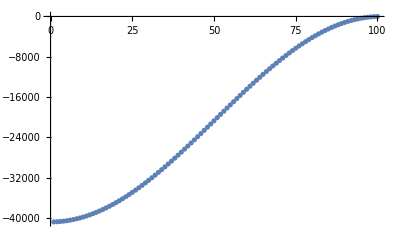

```mathematica
m=100;
A=(m+1)^2 SparseArray[{
Band[{1,1}]->-2,
Band[{1,2}]->1,
Band[{2,1}]->1},{m,m}];
ListPlot[Eigenvalues[A]]
```

For Rabeya’s test problem we should be able to explicitly compare the matrix exponential 
	ⅇ^(A t)y_0	
solution to whatever we get from our approximations.    The large negative eigenvalues (indicating fast time scales for decay) in the same problem as slower time scales are problematic.

## Explicit Euler

The Explicit Euler approximation with a fixed step size h for 
	y'(t)=f(t,y(t))  with y(0)=y_0
is simply
	y_(k+1)=y_k+h f(k h,y_k).
For Rabeya’s test problem y'=A.y we get
	y_1=y_0+h A.y_0
organizing and repeating the process gives
	y_1 | = | (I+h A).y_0
y_2 | = | (I+h A)^2.y_0
  | ⋮ |  
y_k | = | (I+h A)^k.y_0

The question is when does this look like the matrix exponential?

## Implicit Euler

The Implicit Euler approximation aka BDF_1 with a fixed step size h for 
	y'(t)=f(t,y(t))  with y(0)=y_0
is simply
	y_(k+1)=y_k+h f((k+1) h,y_(k+1)).
For Rabeya’s test problem y'=A.y we we get
	y_1=y_0+h A.y_1
or equivalently
	y_1=(I-h A)^-1.y_0
organizing and repeating the process gives
	y_1 | = | (I-h A)^-1.y_0
y_2 | = | (I-h A)^-2.y_0
  | ⋮ |  
y_k | = | (I-h A)^-k.y_0

The question is when does this look like the matrix exponential?

## Trapezoid aka Crank-Nicolson

A trapezoid approximation with a fixed step size h for 
	y'(t)=f(t,y(t))  with y(0)=y_0
is called the Crank-Nicolson scheme in PDE problems.
	y_(k+1)=y_k+h/2 (f(k h,y_k)+f((k+1) h, y_(k+1))).
For Rabeya’s test problem y'=A.y we we get
	y_1=y_0+h/2 (A.y_0+A.y_1)
or equivalently
	y_1=(I-h/2 A)^-1.(I+h/2 A).y_0
organizing and repeating the process gives
	y_1 | = | ((I-h/2 A)^-1.(I+h/2 A))^1.y_0
y_2 | = | ((I-h/2 A)^-1.(I+h/2 A))^2.y_0
  | ⋮ |  
y_k | = | ((I-h/2 A)^-1.(I+h/2 A))^k.y_0
The question is when does this look like the matrix exponential?

## BDF_2 etc.

The BDF_1 (aka Implicit Euler) update formula is  
	(y_(k+1)-y_k)/h= f(t_(k+1),y_(k+1))
The left hand side is just a backwards difference approximation to the derivative.  If we use a slightly fancier approximation to the derivative we get the second of the BDF formula.
	(y_(k+2)-4/3 y_(k+1)+1/3 y_k)/(2/3 h)= f(t_(k+2),y_(k+2)).  
It may well not be obvious that the left hand side is an approximation to the derivative at some appropriate point.  It may be even less obvious that the left hand side of the next one 
	(y_(k+3)-18/11 y_(k+2)+9/11 y_(k+1)-2/11 y_K)/(6/11 h)= f(t_(k+3),y_(k+3))
is a more accurate derivative approximation!

```mathematica
f[t_]:=t+ ArcTan[t+t^2+Cos[Sin[t]]]
h=0.1;
TabView[{
"BDF_1"->Plot[{f'[t+h],(f[t+h]-f[t])/h},{t, 0,3}],
"BDF_2"->Plot[{f'[t+2h],(f[t+2h]-4/3 f[t+h]+1/3 f[t])/(2/3 h)},{t, 0,3}],
"BDF_3"->Plot[{f'[t+3h],(f[t+3h]-18/11 f[t+2h]+9/11 f[t+h]-2/11 f[t])/(6/11 h)},{t, 0,3}]
}]
```

123

We can see the asymptotic behavior.

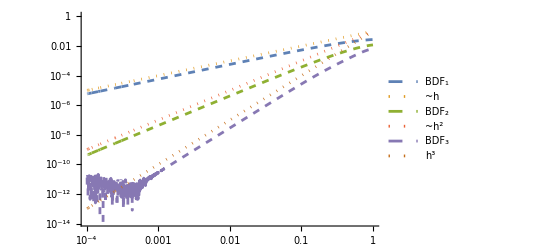

```mathematica
t0=2.1;
LogLogPlot[{
Abs[(f[t0+h]-f[t0])/h-f'[t0+h]],10^-1 h,
Abs[(f[t0+2h]-4/3 f[t0+h]+1/3 f[t0])/(2/3 h)-f'[t0+2h]],10^-1 h^2,
Abs[(f[t0+3h]-18/11 f[t0+2h]+9/11 f[t0+h]-2/11 f[t0])/(6/11 h)-f'[t0+3h]],10^-1 h^3
},{h, 10^-4,1},GridLines->Automatic,
PlotStyle->{Dashed,Dotted},
PlotLegends->{"BDF_1","~h","BDF_2","~h^2","BDF_3","h^3"}]
```

#### Taylor Series verification of error behavior

We can compute the asymptotic behavior using Taylor Series. To keep things tidy I am going to assume the ODE is autonomous. Rewrite the update formulas 
	BDF_1	y_(k+1)-y_k=h f(y_(k+1))
	BDF_2	y_(k+2)-4/3 y_(k+1)+1/3 y_k=2/3 h f(y_(k+2))
	BDF_3	y_(k+3)-18/11 y_(k+2)+9/11 y_(k+1)-2/11 y_K= 6/11 h f(y_(k+3))
about the point inside the function to get
	BDF_1	y_j-y_(j-1)=h f(y_j)
	BDF_2	y_j-4/3 y_(j-1)+1/3 y_(j-2)=2/3 h f(y_j)
	BDF_3	y_j-18/11 y_(j-1)+9/11 y_(j-2)-2/11 y_(j-3)= 6/11 h f(y_j).
If I compute the Taylor series about y_j I should be able to see the asymptotic behavior observed above
	BDF_1	(y_j-y_(j-1))/h=y'(t_j)-1/2 h y''(t_j)+O(h^2)
	BDF_2	(y_j-4/3 y_(j-1)+1/3 y_(j-2))/(2/3 h)=y'(t_j)-1/3 h^2 y^(3)(t_j)+O(h^3)
	BDF_3	(y_j-18/11 y_(j-1)+9/11 y_(j-2)-2/11 y_(j-3))/(6/11 h)= y'(t_j)-1/4 h^3 y^(4)(t_j)+O(h^4).

```mathematica
TraditionalForm[Series[ (y[Subscript[t, j]]-y[Subscript[t, j]-h])/h,{h,0,1}]]
TraditionalForm[Series[ (y[Subscript[t, j]]-4/3 y[Subscript[t, j]-h]+1/3 y[Subscript[t, j]-2h])/(2/3 h),{h,0,2}]]
TraditionalForm[Series[ (y[Subscript[t, j]]-18/11 y[Subscript[t, j]-h]+9/11 y[Subscript[t, j]-2h]-2/11 y[Subscript[t, j]-3h])/(6/11 h),{h,0,3}]]
```

y'(t_j)-1/2 h y''(t_j)+O(h^2)

y'(t_j)-1/3 h^2 y^(3)(t_j)+O(h^3)

y'(t_j)-1/4 h^3 y^(4)(t_j)+O(h^4)

#### Standard Interpolation Construction of BDF.

The polynomials that interpolate the value y_j at time t_j and the back values y_(j-1) at time t_j-h and y_(j-2) at time t_j-2h etc are
 	BDF_1	p_1(t)=y_j-((t-t_j) (y_(j-1)-y_j))/h
	BDF_2	p_2(t)= (t-t_j) (-((h-t_j+t) ((y_(j-1)-y_j)/h-(y_(j-2)-y_(j-1))/h))/(2 h)-(y_(j-1)-y_j)/h)+y_j
	BDF_3	p_3(t)=(t-t_j) ((h-t_j+t) (-((2 h-t_j+t) (((y_(j-1)-y_j)/h-(y_(j-2)-y_(j-1))/h)/(2 h)-((y_(j-2)-y_(j-1))/h-(y_(j-3)-y_(j-2))/h)/(2 h)))/(3 h)-((y_(j-1)-y_j)/h-(y_(j-2)-y_(j-1))/h)/(2 h))-(y_(j-1)-y_j)/h)+y_j
Evaluating the derivatives of these at t=t_j gives the BDF coefficients!
	BDF_1	p_1'(t_j)=(y_j-y_(j-1))/h
	BDF_2	p_2'(t_j)= (y_(j-2) - 4 y_(j-1)+3 y_j)/(2 h)
	BDF_3	p_3'(t_j)=(-2 y_(j-3)+9 y_(j-2)-18 y_(j-1)+11 y_j)/(6 h)
You could (if you wanted to) work out the higher order BDF formulas the same way.